# Comportamento de Diversos Circuitos de Transmissão em Regime Permanente

## Antonio Carlos Siqueira de Lima Maio 2023

## Inicialização

```mathematica
Clear["Global`*"]
```

```mathematica
SetDirectory[NotebookDirectory[]]
```

/Users/acsl/Dropbox/UFRJ/cursos/EEE457-Transmissão_Energia_Elétrica/arquivos_Mma_EEE457

```mathematica
SetOptions[{Plot,LogPlot,LogLinearPlot,LogLogPlot},BaseStyle->{FontFamily->"Helvetica", 14},ImageSize-> 600,PlotStyle-> Thick,Axes-> False,Frame-> True];
```

## Definição das funções

Quadripolo da linha curta

```mathematica
qlc[z_, ℓ_]:={{1, z ℓ},{0,1}}
```

Quadripolo da linha média

```mathematica
qlm[z_,y_,ℓ_]:={{1, 0},{y ℓ/2,1}}.{{1, z ℓ},{0,1}}.{{1, 0},{y ℓ/2,1}}
```

Quadripolo da linha longa

```mathematica
qll[z_,y_,ℓ_]:=With[{γ=Sqrt[z y], Zc=Sqrt[z/y]}, 
{{Cosh[γ ℓ], Zc Sinh[γ ℓ]},{1/Zc Sinh[γ ℓ],Cosh[γ ℓ]}}]
```

## Verificação de sanidade

```mathematica
Det[qlc[z,ℓ]]
```

1

```mathematica
Det[qlm[z,y,ℓ]]
```

1

```mathematica
Det[qll[z,y,ℓ]]
```

Cosh[√(y z) ℓ]^2-Sinh[√(y z) ℓ]^2

```mathematica
FullSimplify[Cosh[√(y z) ℓ]^2-Sinh[√(y z) ℓ]^2]
```

1

## Configurações analisadas

### Circuito de 69 kV (069 CST1)

Condições operativas

```mathematica
vr = 69./Sqrt[3] 10^3;
```

Dados do circuitos (condutor Linnet)

```mathematica
z = 0.1914 + I 0.438;
y = I 3.4276 10^-6;
```

supondo carregamento igual a impedância característica

```mathematica
zc= Sqrt[z/y];
ir= vr/zc
```

104.422+21.8194 ⅈ

Para comprimento igual a 80 km

```mathematica
{vs1, is1}=qlc[z, 80].{vr, ir};
```

```mathematica
vs1/vr
```

1.02094+0.100234 ⅈ

```mathematica
Abs[vs1]/(vr)
```

1.02585

```mathematica
Arg[vs1]/π 180
```

5.60722

```mathematica
{vs2, is2}=qll[z,y, 80].{vr, ir};
```

```mathematica
vs2/vs1
```

0.995428+0.00235907 ⅈ

```mathematica
Arg[vs2]/π 180
```

5.743

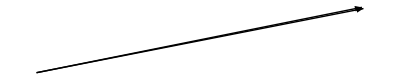

```mathematica
Graphics[{Arrow[{{0,0},{Re[vs1],Im[vs1]}}],Arrow[{{0,0},{Re[vs2],Im[vs2]}}]}]
```

### Circuito de 69 kV (069 CST1)

Condições operativas máximas

```mathematica
vr1 =1.05 69./Sqrt[3] 10^3;
```

Dados do circuitos (condutor Linnet)

```mathematica
z = 0.1914 + I 0.438;
y = I 3.4276 10^-6;
```

supondo carregamento igual a impedância característica

```mathematica
zc= Sqrt[z/y];
ir1= vr1/(2zc)
```

54.8216+11.4552 ⅈ

Para comprimento igual a 80 km

```mathematica
{vs3, is3}=qlc[z, 80].{vr1, ir1};
```

```mathematica
vs3/vr1
```

1.01047+0.0501171 ⅈ

```mathematica
Abs[vs3]/(vr1)
```

1.01171

```mathematica
{vs4, is4}=qll[z,y, 80].{vr1, ir1};
```

```mathematica
vs4/vs3
```

0.995308+0.0022348 ⅈ

```mathematica
Arg[vs3]/π 180
```

2.83941

```mathematica
Arg[vs4]/π 180
```

2.96806

```mathematica
Abs[vs4]/vr
```

1.05732

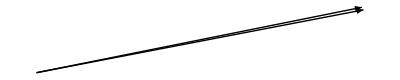

```mathematica
Graphics[{Arrow[{{0,0},{Re[vs3],Im[vs3]}}],Arrow[{{0,0},{Re[vs4],Im[vs4]}}]}]
```

### Circuito de 69 kV (069 CST1) corrente nominal do cabo

Condições operativas

```mathematica
vr2 = 69./Sqrt[3] 10^3;
ir2 = 435.;
```

Dados do circuitos (condutor Linnet)

```mathematica
z = 0.1914 + I 0.438;
y = I 3.4276 10^-6;
```

supondo carregamento igual a impedância característica

```mathematica
zc= Sqrt[z/y];
```

Reduzindo o comprimento para 20 km

```mathematica
{vs5, is5}=qlc[z, 20].{vr2, ir2};
```

```mathematica
vs5/vr
```

1.0418+0.0956544 ⅈ

```mathematica
Abs[vs5]/(vr)
```

1.04618

```mathematica
Arg[vs5]/π 180
```

5.24599

```mathematica
{vs6, is6}=qll[z,y, 20].{vr2, ir2};
```

```mathematica
Abs[vs6]/vr
```

1.04589

```mathematica
Arg[vs2]/π 180
```

5.743

```mathematica
vr ir
```

4.15988×10^6+869222. ⅈ

## Exercício

Supondo Is= 435 A (com fator de potência unitário) calcule Ir e Vs, supondo que 0,95<= Vr <= 1,05

```mathematica
vr3 = 69./Sqrt[3] 10^3;
is3 = 435.;
```

```mathematica
{vss, is3}=qll[z,y, 20].{vr3, irr}
```

{(39825.2+5.22645 ⅈ)+(3.82723+8.75929 ⅈ) irr,(-0.000119433+2.73064 ⅈ)+(0.9997+0.000131195 ⅈ) irr}

### Circuito de 138 kV (138 CST1) condutor Dove

```mathematica
vr = 138/Sqrt[3] 10^3;
z= 0.1160+I 0.4821;
y=I  3.4379 10^-6;
```

```mathematica
zc=Sqrt[z/y]
```

377.137-44.7338 ⅈ

```mathematica
ir =vr/zc
```

208.33+24.7109 ⅈ

```mathematica
{vs, is}=qll[z,y, 80].{1.04vr,  ir};
```

```mathematica
Abs[vs]/vr
```

1.05197

### Circuito de 230 kV (230CH1) condutor Grossbeak

```mathematica
vr = 230/Sqrt[3] 10^3;
z=0.0510 +I 0.3339;
y= 4.96040 10^-6;
zc= Sqrt[z/y];
ir =vr/zc
```

386.042-331.555 ⅈ

```mathematica
(3 vr^2/Re[zc])/10^6
```

267.228

```mathematica
Abs[ir]
```

508.878

```mathematica
{vs, is}=qll[z,y, 80].{ 1.05vr, ir};
```

```mathematica
1.05 vr ir
```

5.38258×10^7-4.62287×10^7 ⅈ

```mathematica
vs/vr
```

1.1293+0.0731922 ⅈ